Figure for amperesLawBetweenTwoCurrents.eps.  Circles surrounding two currents, with respective phicap vectors around those sources.

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16];
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

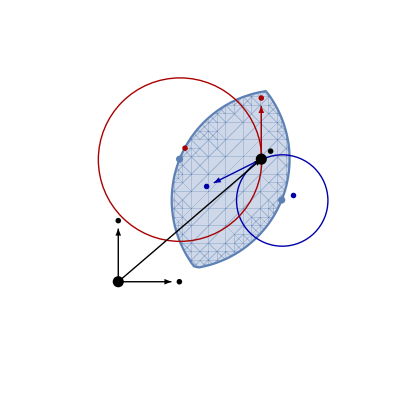

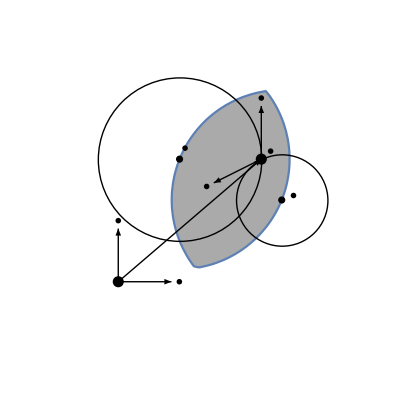

```mathematica
ClearAll[o,e1,e1,stuff, bwstuff,bold, boldsubx, te, rot90, amperesLawBetweenTwoCurrentsFig1, bwamperesLawBetweenTwoCurrentsFig1, subx]
o = {0,0};
{e1,e2} = IdentityMatrix[2];

rot90 = RotationMatrix[Pi/2];

(*bold = Style[ #, Bold] &;
fs = Style[ #, FontSize->16]&;*)
bold = MaTeX[ "\\mathbf{"<>#<>"}"] &;
boldsubx[x_, i_, s_ : "_"] := (MaTeX[ "\\mathbf{" <> x <>"}" <>s <> ToString[i]] ) ;
subx[x_, i_, s_ : "_"] := (MaTeX[ x <>"" <>s <> ToString[i]] ) ;
te[n_] := boldsubx["e", n];

stuff[center_, boundingPt_, idx_, color_, lcolor_,one_] := Module[{radius,r,rcap, phicap},
r = boundingPt - center;
rcap = r // Normalize;
phicap = rot90.rcap;
radius = r// Norm;
{
color,
Thick,
Circle[center,radius],
Text[subx["I", idx],center + 0.15 Normalize[center]],
Arrow[ {boundingPt, boundingPt + phicap one}],
Text[subx["\\color{"<>lcolor<>"}\\hat{\\boldsymbol{\\phi}}", idx],boundingPt + phicap one 1.15]
}];
bwstuff[center_, boundingPt_, idx_, one_] := Module[{radius,r,rcap, phicap},
r = boundingPt - center;
rcap = r // Normalize;
phicap = rot90.rcap;
radius = r// Norm;
{

Thick,
Circle[center,radius],
Text[subx["I", idx],center + 0.15 Normalize[center]],
Arrow[ {boundingPt, boundingPt + phicap one}],
Text[subx["\\hat{\\boldsymbol{\\phi}}", idx],boundingPt + phicap one 1.15]
}];

amperesLawBetweenTwoCurrentsFig1 = Module[{p1,p2,(*p3,*)r, range, one, rr, range2},
p1 = {2,1};
p2 = {1,2}0.75;
rr = Norm[p1-p2];
(*p3 = {2,2};*)
r = {1.75,1.5};
range = {-0.5,2.75};
range2 = 10;
one = 0.65;
Show[{

RegionPlot[
(x-p1[[1]])^2+(y-p1[[2]])^2<rr^2 &&
(x-p2[[1]])^2+(y-p2[[2]])^2<rr^2
,{x,-1,3},{y,-1,3}, Ticks -> None, Frame -> None(*, PlotStyle->Thick*)],
ListPlot[ {p1, p2}, AspectRatio -> 1, PlotRange->{range,range}, Ticks -> None, PlotStyle->Thick],
Graphics[
Flatten[
{
 stuff[p1,r,1,Blue//Darker, "BlueDarker",one],
 stuff[p2,r,2,Red// Darker, "RedDarker",one],
{
Black,
Arrow[{o,r}],
Arrow[{o,e1 one}],
Arrow[{o,e2 one}],
Text["r" // bold , r + 0.15 Normalize[r]],
Text[te[ 1],e1 one 1.15],
Text[te[ 2],e2 one 1.15],

PointSize->0.02,
Point[{o,r}]
}
},
1]
]
}]
]

bwamperesLawBetweenTwoCurrentsFig1 = Module[{p1,p2,(*p3,*)r, range, one, rr, range2},
p1 = {2,1};
p2 = {1,2}0.75;
rr = Norm[p1-p2];
(*p3 = {2,2};*)
r = {1.75,1.5};
range = {-0.5,2.75};
range2 = 10;
one = 0.65;
Show[{

RegionPlot[
(x-p1[[1]])^2+(y-p1[[2]])^2<rr^2 &&
(x-p2[[1]])^2+(y-p2[[2]])^2<rr^2
,{x,-1,3},{y,-1,3}, Ticks -> None, Frame -> None, PlotStyle->{Gray // Lighter}],
ListPlot[ {p1, p2}, AspectRatio -> 1, PlotRange->{range,range}, Ticks -> None, PlotStyle->{Thick, Black}],
Graphics[
Flatten[
{
 bwstuff[p1,r,1,one],
 bwstuff[p2,r,2,one],
{
Black,
Arrow[{o,r}],
Arrow[{o,e1 one}],
Arrow[{o,e2 one}],
Text["r" // bold , r + 0.15 Normalize[r]],
Text[te[ 1],e1 one 1.15],
Text[te[ 2],e2 one 1.15],

PointSize->0.02,
Point[{o,r}]
}
},
1]
]
}]
]
```

```mathematica
peeters`exportForLatex["color/amperesLawBetweenTwoCurrentsFig1", amperesLawBetweenTwoCurrentsFig1]
peeters`exportForLatex["bw/amperesLawBetweenTwoCurrentsFig1", bwamperesLawBetweenTwoCurrentsFig1]
```

{color/amperesLawBetweenTwoCurrentsFig1.eps,color/amperesLawBetweenTwoCurrentsFig1pn.png}

{bw/amperesLawBetweenTwoCurrentsFig1.eps,bw/amperesLawBetweenTwoCurrentsFig1pn.png}